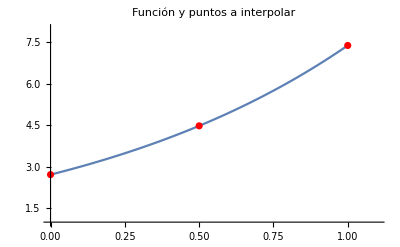

```mathematica
f[x_]=Exp[x+1];
puntos=ListPlot[{{0,f[0]},{0.5,f[0.5]},{1,f[1]}}, PlotStyle->Red];
grafica = Plot[f[x],{x,0,1}, PlotLabel->Style["Función y puntos a interpolar", FontSize->16, Black], PlotRange->{{0,1.1},{1,8}}];
Show[grafica,puntos]
```

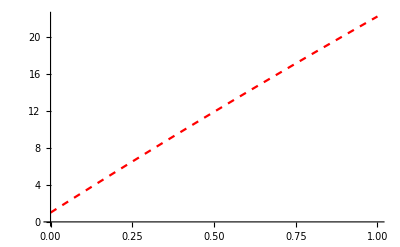

```mathematica
polinomio[x_] = (2 Exp[0]-4 Exp[1.5]+2Exp[2])x^2+(-3 Exp[0]+4 Exp[1.5]+Exp[2])x+Exp[0];
gpolinomio = Plot[polinomio[x],{x,0,1},PlotStyle->{Dashed,Red}]
```

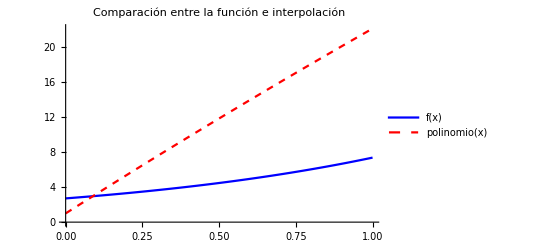

```mathematica
Plot[{f[x], polinomio[x]},{x,0,1}, PlotStyle->{{Blue},{Red, Dashed}}, PlotLabel->Style["Comparación entre la función e interpolación", FontSize->16, Black], PlotLegends->"Expressions"]
```

```mathematica
a =N[(2 Exp[0]-4 Exp[1.5]+2Exp[2])]
```

-1.14864

```mathematica
b =N[-3 Exp[0]+4 Exp[1.5]+Exp[2]]
```

22.3158

```mathematica
c = N[Exp[0]]
```

1.

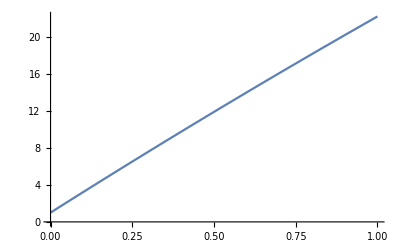

```mathematica
Plot[a x^2+b x+ c, {x,0,1}]
```